## Now with 4 nodes

```mathematica
gen4=Monitor[Select[Keys[allGraphs4],With[{k=#},VertexCount[allGraphs4[#,"graph"]]==4&&Length[FlatGenerators[allGraphs4[#,"colofour"]]]==1]&],k];Length[gen4]
```

15

```mathematica
prob=Table[Symbol["g"<>StringDrop[SymbolName[First[FlatGenerators[allGraphs4[k,"colofour"]]]],1]]==allGraphs4[k,"colofour"],{k,gen4}];
gen4Symbols=Sort[Table[Symbol["g"<>StringDrop[SymbolName[First[FlatGenerators[allGraphs4[k,"colofour"]]]],1]],{k,gen4}],CompareSymbols];
```

```mathematica
rep4=First[Solve[prob,Table[allGraphs4[k,"colofour"],{k,allGraphs4AtomKeys}]]];
gen4Coeff[form_]:=Table[Coefficient[form,term],{term, gen4Symbols}]
fullSym=Sort[Table[allGraphs4[k,"colofour"],{k,allGraphs4AtomKeys}],CompareSymbols];
```

```mathematica
Monitor[Table [allGraphs4[k,"genfour"]=Simplify[allGraphs4[k,"colofour"]/.rep4],{k,Keys[allGraphs4]}],k];
```

```mathematica
full4Coeff[form_]:=Table[Coefficient[form,term],{term, fullSym}]
```

```mathematica
fullSym5=Sort[Table[allGraphs5[k,"colofour"],{k,allGraphs5AtomKeys}],CompareSymbols]
```

{v1x2x3x4x5,v1x2x3x45,v1x2x34x5,v1x2x35x4,v1x23x4x5,v1x24x3x5,v1x25x3x4,v12x3x4x5,v13x2x4x5,v14x2x3x5,v15x2x3x4,v1x23x45,v1x24x35,v1x25x34,v12x3x45,v12x34x5,v12x35x4,v13x2x45,v13x24x5,v13x25x4,v14x2x35,v14x23x5,v14x25x3,v15x2x34,v15x23x4,v15x24x3,v1x2x345,v1x234x5,v1x235x4,v1x245x3,v123x4x5,v124x3x5,v125x3x4,v134x2x5,v135x2x4,v145x2x3,v12x345,v123x45,v124x35,v125x34,v13x245,v134x25,v135x24,v14x235,v145x23,v15x234,v1x2345,v1234x5,v1235x4,v1245x3,v1345x2,v12345}

```mathematica
full5Coeff[form_]:=Table[Coefficient[form,term],{term, fullSym5}]
```

```mathematica
gen4Sorted=Sort[gen4,CompareSymbols[allGraphs4[#1,"genfour"],allGraphs4[#2,"genfour"]]&]
```

{364,363,355,361,121,283,337,120,280,328,351,31,91,255,0}

```mathematica
gen5Sorted=Sort[gen5,CompareSymbols[allGraphs5[#1,"genfour"],allGraphs5[#2,"genfour"]]&]
```

{29524,29523,29515,29521,29281,29443,29497,9841,22963,27337,28795,29280,29440,29488,9840,9832,9838,22962,22882,22936,27334,27094,27310,28786,28552,28714,29511,29191,29251,29415,3037,7573,9085,20767,22231,26607,9828,3036,7570,9076,22854,20740,22150,27064,26364,28462,29160,760,2278,6816,20034,0}

```mathematica
fullSorted=Sort[allGraphs4AtomKeys,CompareSymbols[allGraphs4[#1,"colofour"],allGraphs4[#2,"colofour"]]&]
```

{364,365,373,367,607,445,391,608,448,400,377,697,637,473,728}

```mathematica
Intersection[gen4Sorted,fullSorted]
```

{364}

```mathematica
allGraphs4[7174453,"graph"]
```

Missing[KeyAbsent,7174453]

-Graphics-

```mathematica
Table[allGraphs4[k,"genfour"],{k,allGraphs4AtomKeys}]
```

{g1x2x3x4,g1x2x34-g1x2x3x4,g1x24x3-g1x2x3x4,g1x23x4-g1x2x3x4,g1x234-g1x23x4-g1x24x3-g1x2x34+2 g1x2x3x4,g14x2x3-g1x2x3x4,g14x23-g14x2x3-g1x23x4+g1x2x3x4,g13x2x4-g1x2x3x4,g13x24-g13x2x4-g1x24x3+g1x2x3x4,g134x2-g13x2x4-g14x2x3-g1x2x34+2 g1x2x3x4,g12x3x4-g1x2x3x4,g12x34-g12x3x4-g1x2x34+g1x2x3x4,g124x3-g12x3x4-g14x2x3-g1x24x3+2 g1x2x3x4,g123x4-g12x3x4-g13x2x4-g1x23x4+2 g1x2x3x4,g1234-g123x4-g124x3-g12x34+2 g12x3x4-g134x2-g13x24+2 g13x2x4-g14x23+2 g14x2x3-g1x234+2 g1x23x4+2 g1x24x3+2 g1x2x34-6 g1x2x3x4}

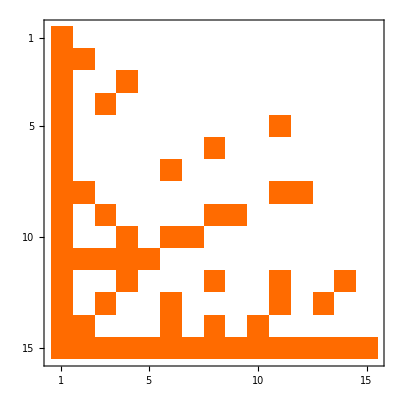

```mathematica
Table[gen4Coeff[allGraphs4[k,"genfour"]],{k,allGraphs4AtomKeys}]//Inverse//MatrixPlot
```

```mathematica
allGraphs4[K4Key,"genfour"]
```

g1x2x3x4

```mathematica
Monitor[Table[Length[allGraphs4[k,"genfour"]],{k,Keys[allGraphs4]}],k]//Tally//Sort
```

{{0,15},{2,12},{3,39},{4,19},{5,4},{7,12},{8,6},{10,6},{11,6},{14,7},{15,1}}

```mathematica
Table[allGraphs4[k,"genfour"],{k,{0,K4Key,K5Key}}]
```

{g1234,g1x2x3x4,Missing[KeyAbsent,29524]}

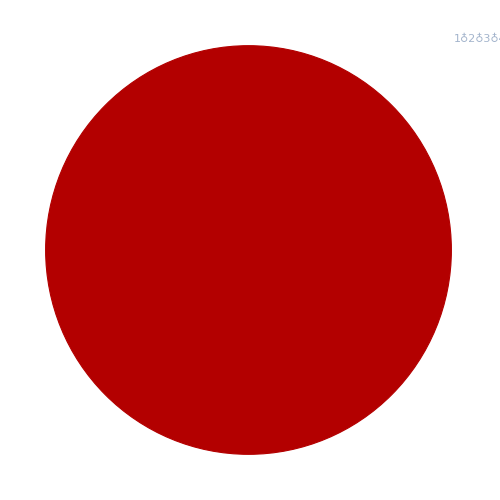
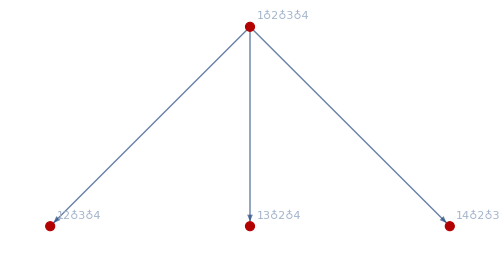

```mathematica
Table[Graph[FormulaGraph[allGraphs4[k,"colofour"]],GraphHighlight->VertexList[FormulaGraph[allGraphs4[k,"genfour"]]],ImageSize->500],{k,{K4Key,K3Key}}]
```

```mathematica
repGen4=Table[allGraphs4[k,"genfour"]->
Graph[CompleteGraph[4],GraphHighlight->EdgeList[GraphComplement[allGraphs4[k,"graph"]]],VertexLabels->"Name",VertexStyle->Red,EdgeStyle->Blue,GraphHighlightStyle->{"Thick"},ImageSize->50]
,{k,gen4}];
```

```mathematica
repFull4=Table[allGraphs4[k,"colofour"]->
ShowGraph[allGraphs4,k]
,{k,allGraphs4AtomKeys}];
```

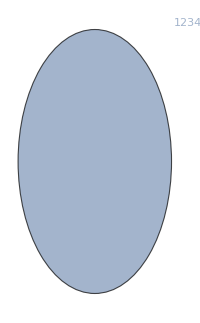
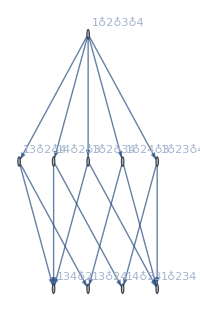
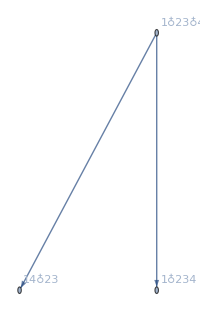
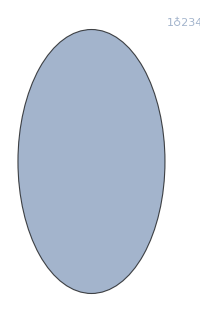
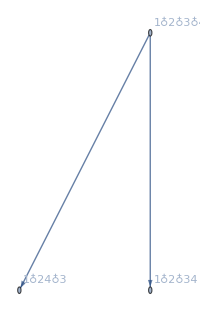
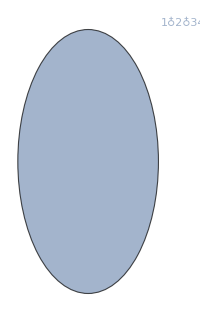
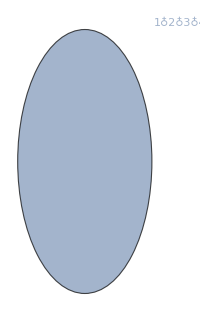
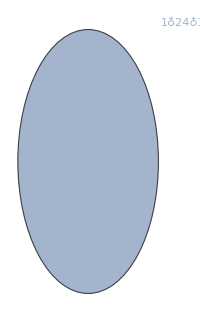
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-728+-Graphics-697+-Graphics-637+-Graphics-608+-Graphics-473+-Graphics-400+-Graphics-377+-Graphics-448+-Graphics-607+-Graphics-445+-Graphics-373+-Graphics-391+-Graphics-367+-Graphics-365+-Graphics-364},{-Graphics-,-Graphics-,2 -Graphics---Graphics---Graphics---Graphics---Graphics---Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-,-Graphics-473+-Graphics-400+-Graphics-377+-Graphics-448+-Graphics-445+-Graphics-373+-Graphics-391+-Graphics-367+-Graphics-365+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-400+-Graphics-377+-Graphics-373+-Graphics-391+-Graphics-367+-Graphics-365+-Graphics-364},{-Graphics-,-Graphics-,-Graphics-,-Graphics-377+-Graphics-373+-Graphics-367+-Graphics-365+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-367+-Graphics-365+-Graphics-364},{-Graphics-,-Graphics-,-Graphics-,-Graphics-365+-Graphics-364},{-Graphics-,-Graphics-,-Graphics-,-Graphics-364},{-Graphics-,-Graphics-,-Graphics-,-Graphics-367+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-373+-Graphics-365+-Graphics-364},{-Graphics-,-Graphics-,-Graphics-,-Graphics-373+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-373+-Graphics-367+-Graphics-364},{-Graphics-,-Graphics-,-2 -Graphics-+-Graphics-+-Graphics-+-Graphics-,-Graphics-391+-Graphics-367+-Graphics-365+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-391+-Graphics-365+-Graphics-364},{-Graphics-,-Graphics-,-Graphics-,-Graphics-391+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-391+-Graphics-367+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-400+-Graphics-373+-Graphics-391+-Graphics-365+-Graphics-364},{-Graphics-,-Graphics-,-Graphics-,-Graphics-400+-Graphics-373+-Graphics-391+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-400+-Graphics-373+-Graphics-391+-Graphics-367+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-377+-Graphics-448+-Graphics-445+-Graphics-373+-Graphics-367+-Graphics-365+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-448+-Graphics-445+-Graphics-367+-Graphics-365+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-445+-Graphics-365+-Graphics-364},{-Graphics-,-Graphics-,-Graphics-,-Graphics-445+-Graphics-364},{-Graphics-,-Graphics-,-Graphics-,-Graphics-448+-Graphics-445+-Graphics-367+-Graphics-364},{-Graphics-,-Graphics-,-2 -Graphics-+-Graphics-+-Graphics-+-Graphics-,-Graphics-445+-Graphics-373+-Graphics-365+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-445+-Graphics-373+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-448+-Graphics-445+-Graphics-373+-Graphics-367+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-473+-Graphics-448+-Graphics-445+-Graphics-391+-Graphics-367+-Graphics-365+-Graphics-364},{-Graphics-,-Graphics-,-Graphics-,-Graphics-473+-Graphics-445+-Graphics-391+-Graphics-365+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-445+-Graphics-391+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-448+-Graphics-445+-Graphics-391+-Graphics-367+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-473+-Graphics-400+-Graphics-445+-Graphics-373+-Graphics-391+-Graphics-365+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-400+-Graphics-445+-Graphics-373+-Graphics-391+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-400+-Graphics-448+-Graphics-445+-Graphics-373+-Graphics-391+-Graphics-367+-Graphics-364},{-Graphics-,-Graphics-,2 -Graphics---Graphics---Graphics---Graphics---Graphics---Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-,-Graphics-637+-Graphics-608+-Graphics-400+-Graphics-377+-Graphics-607+-Graphics-373+-Graphics-391+-Graphics-367+-Graphics-365+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-608+-Graphics-377+-Graphics-607+-Graphics-373+-Graphics-367+-Graphics-365+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-608+-Graphics-607+-Graphics-367+-Graphics-365+-Graphics-364},{-Graphics-,-Graphics-,-Graphics-,-Graphics-608+-Graphics-607+-Graphics-365+-Graphics-364},{-Graphics-,-Graphics-,-Graphics-,-Graphics-607+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-607+-Graphics-367+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-608+-Graphics-607+-Graphics-373+-Graphics-365+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-607+-Graphics-373+-Graphics-364},{-Graphics-,-Graphics-,-2 -Graphics-+-Graphics-+-Graphics-+-Graphics-,-Graphics-607+-Graphics-373+-Graphics-367+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-637+-Graphics-608+-Graphics-607+-Graphics-391+-Graphics-367+-Graphics-365+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-608+-Graphics-607+-Graphics-391+-Graphics-365+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-607+-Graphics-391+-Graphics-364},{-Graphics-,-Graphics-,-Graphics-,-Graphics-637+-Graphics-607+-Graphics-391+-Graphics-367+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-608+-Graphics-400+-Graphics-607+-Graphics-373+-Graphics-391+-Graphics-365+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-400+-Graphics-607+-Graphics-373+-Graphics-391+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-637+-Graphics-400+-Graphics-607+-Graphics-373+-Graphics-391+-Graphics-367+-Graphics-364},{-Graphics-,-Graphics-,2 -Graphics---Graphics---Graphics---Graphics---Graphics---Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-,-Graphics-697+-Graphics-608+-Graphics-377+-Graphics-448+-Graphics-607+-Graphics-445+-Graphics-373+-Graphics-367+-Graphics-365+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-608+-Graphics-448+-Graphics-607+-Graphics-445+-Graphics-367+-Graphics-365+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-608+-Graphics-607+-Graphics-445+-Graphics-365+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-607+-Graphics-445+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-448+-Graphics-607+-Graphics-445+-Graphics-367+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-697+-Graphics-608+-Graphics-607+-Graphics-445+-Graphics-373+-Graphics-365+-Graphics-364},{-Graphics-,-Graphics-,-Graphics-,-Graphics-697+-Graphics-607+-Graphics-445+-Graphics-373+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-697+-Graphics-448+-Graphics-607+-Graphics-445+-Graphics-373+-Graphics-367+-Graphics-364},{-Graphics-,-Graphics-,2 -Graphics---Graphics---Graphics---Graphics---Graphics---Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-,-Graphics-637+-Graphics-608+-Graphics-473+-Graphics-448+-Graphics-607+-Graphics-445+-Graphics-391+-Graphics-367+-Graphics-365+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-608+-Graphics-473+-Graphics-607+-Graphics-445+-Graphics-391+-Graphics-365+-Graphics-364},{-Graphics-,-Graphics-,-2 -Graphics-+-Graphics-+-Graphics-+-Graphics-,-Graphics-607+-Graphics-445+-Graphics-391+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-637+-Graphics-448+-Graphics-607+-Graphics-445+-Graphics-391+-Graphics-367+-Graphics-364},{-Graphics-,-Graphics-,2 -Graphics---Graphics---Graphics---Graphics---Graphics---Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-,-Graphics-697+-Graphics-608+-Graphics-473+-Graphics-400+-Graphics-607+-Graphics-445+-Graphics-373+-Graphics-391+-Graphics-365+-Graphics-364},{-Graphics-,-Graphics-,--Graphics-+-Graphics-+-Graphics-,-Graphics-697+-Graphics-400+-Graphics-607+-Graphics-445+-Graphics-373+-Graphics-391+-Graphics-364},{-Graphics-,-Graphics-,2 -Graphics---Graphics---Graphics---Graphics---Graphics---Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-,-Graphics-697+-Graphics-637+-Graphics-400+-Graphics-448+-Graphics-607+-Graphics-445+-Graphics-373+-Graphics-391+-Graphics-367+-Graphics-364}}

```mathematica
Table[{allGraphs4[k,"graph"],Graph[FormulaGraph[allGraphs4[k,"genfour"]],ImageSize->200,AspectRatio->GoldenRatio],TraditionalForm[allGraphs4[k,"genfour"]/.repGen4],allGraphs4[k,"colofour"]/.repFull4},{k,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&]}]
```